```mathematica
Exit[];
```

## Part 1a

Let' s take the two-level system as an example to do the calculation. Here, the symbols are defined as follows:
(a_(1+))^†----> a1pd,
a_(1+)----> a1p,
(a_(1-))^†---->a1md,
a_(1-)---->a1m. 
Similar conventions for the second particle.

```mathematica
Sz=1/2(a1pd ⊙a1p + a2pd⊙a2p - a1md⊙a1m- a2md⊙a2m)//Expand;
Sp=a1pd⊙a1m +a2pd⊙a2m;
Sm=a1md⊙a1p + a2md⊙a2p;
S2=Sz⊙Sz+1/2 Sp⊙Sm+1/2 Sm⊙Sp;
H0=a2pd⊙a2p+a2md⊙a2m;
P1p=a1pd⊙a1md;
P1m=a1p⊙a1m;
P2p=a2pd⊙a2md;
P2m=a2p⊙a2m;
V=P1p⊙P1m+P1p⊙P2m+P2p⊙P1m+P2p⊙P2m;
```

```mathematica
Rules4SecondQuantizationSimplification={a___⊙(b_ +c_)⊙d___:> a⊙b⊙d+a⊙c⊙d,a___⊙(b_+c_)⊙d___:>a⊙b⊙d+a⊙c⊙d,CircleDot[Times[a_,b___],c___]/;a ∈Reals:> a CircleDot[b,c],CircleDot[c___,Times[a_,b___],d___]/;a ∈Reals:> a CircleDot[c,b,d],CircleDot[a___,CircleDot[b__],c___]:>CircleDot[a,b,c],CircleDot[a_,b___]/;a ∈Reals:> a CircleDot[b],
(*Nontrivial anticommutations*)
a___⊙a1m⊙a1md⊙b___:>-a⊙a1md⊙a1m⊙b+a⊙b,a___⊙a2m⊙a2md⊙b___:>-a⊙a2md⊙a2m⊙b+a⊙b,a___⊙a1p⊙a1pd⊙b___:>-a⊙a1pd⊙a1p⊙b+a⊙b,a___⊙a2p⊙a2pd⊙b___:>-a⊙a2pd⊙a2p⊙b+a⊙b,
(*Vanishing dot products*)
a___⊙a1m⊙a1m⊙b___:>0,a___⊙a1p⊙a1p⊙b___:>0,a___⊙a2m⊙a2m⊙b___:>0,a___⊙a2p⊙a2p⊙b___:>0,a___⊙a1md⊙a1md⊙b___:>0,a___⊙a1pd⊙a1pd⊙b___:>0,a___⊙a2md⊙a2md⊙b___:>0,a___⊙a2pd⊙a2pd⊙b___:>0,
(*Move dagger forward*)
a___⊙a1p⊙a1md⊙b___:>-a⊙a1md⊙a1p⊙b,
a___⊙a1p⊙a2pd⊙b___:>-a⊙a2pd⊙a1p⊙b,
a___⊙a1p⊙a2md⊙b___:>-a⊙a2md⊙a1p⊙b,
a___⊙a1m⊙a1pd⊙b___:>-a⊙a1pd⊙a1m⊙b,
a___⊙a1m⊙a2pd⊙b___:>-a⊙a2pd⊙a1m⊙b,
a___⊙a1m⊙a2md⊙b___:>-a⊙a2md⊙a1m⊙b,
a___⊙a2p⊙a1md⊙b___:>-a⊙a1md⊙a2p⊙b,
a___⊙a2p⊙a1pd⊙b___:>-a⊙a1pd⊙a2p⊙b,
a___⊙a2p⊙a2md⊙b___:>-a⊙a2md⊙a2p⊙b,
a___⊙a2m⊙a1pd⊙b___:>-a⊙a1pd⊙a2m⊙b,
a___⊙a2m⊙a1md⊙b___:>-a⊙a1md⊙a2m⊙b,
a___⊙a2m⊙a2pd⊙b___:>-a⊙a2pd⊙a2m⊙b,
(*Move the first particle forward*)
a___⊙a2p⊙a1p⊙b___:>-a⊙a1p⊙a2p⊙b,
a___⊙a2p⊙a1m⊙b___:>-a⊙a1m⊙a2p⊙b,
a___⊙a2m⊙a1p⊙b___:>-a⊙a1p⊙a2m⊙b,
a___⊙a2m⊙a1m⊙b___:>-a⊙a1m⊙a2m⊙b,
a___⊙a2pd⊙a1pd⊙b___:>-a⊙a1pd⊙a2pd⊙b,
a___⊙a2pd⊙a1md⊙b___:>-a⊙a1md⊙a2pd⊙b,
a___⊙a2md⊙a1pd⊙b___:>-a⊙a1pd⊙a2md⊙b,
a___⊙a2md⊙a1md⊙b___:>-a⊙a1md⊙a2md⊙b,
(*Move the + state forward*)
a___⊙a1m⊙a1p⊙b___:>-a⊙a1p⊙a1m⊙b,
a___⊙a2m⊙a2p⊙b___:>-a⊙a2p⊙a2m⊙b,
a___⊙a1md⊙a1pd⊙b___:>-a⊙a1pd⊙a1md⊙b,
a___⊙a2md⊙a2pd⊙b___:>-a⊙a2pd⊙a2md⊙b,
(*Auxiliary Rules*)
CircleDot[]->1
};
```

```mathematica
S2=(S2//.Rules4SecondQuantizationSimplification//Expand);
```

```mathematica
Sz⊙S2-S2⊙Sz//.Rules4SecondQuantizationSimplification//Expand
```

0

```mathematica
Sz⊙H0-H0⊙Sz//.Rules4SecondQuantizationSimplification//Expand
```

0

```mathematica
S2⊙H0-H0⊙S2//.Rules4SecondQuantizationSimplification//Expand
```

0

```mathematica
Sz⊙V-V⊙Sz//.Rules4SecondQuantizationSimplification//Expand
```

0

```mathematica
S2⊙V-V⊙S2//.Rules4SecondQuantizationSimplification//Expand
```

0

```mathematica
(P1p⊙P1m+P2p⊙P2m)⊙(H0+V)-(H0+V)⊙(P1p⊙P1m+P2p⊙P2m)//.Rules4SecondQuantizationSimplification//Expand
```

0

## Part 1b

```mathematica
SingleParticleStatesCreation={a1pd,a1md,a2pd,a2md};
SingleParticleStatesAnnihilation={a1p,a1m,a2p,a2m};
```

```mathematica
TwoParticleStatesCreation=CircleDot@@@(Subsets[SingleParticleStatesCreation,{2}]);
TwoParticleStatesAnnihilation=CircleDot@@@(Subsets[SingleParticleStatesAnnihilation,{2}])/.{a_⊙b_:>b⊙a};
```

```mathematica
Rules4HamiltonianMatrixSimplification={a___⊙a1p:> 0,a___⊙a2p:> 0,a___⊙a1m:> 0,a___⊙a2m:> 0,a1pd⊙a___:>0,a2pd⊙a___:>0,a1md⊙a___:>0,a2md⊙a___:>0};
```

```mathematica
TwoParticleStatesCreation
```

{a1pd⊙a1md,a1pd⊙a2pd,a1pd⊙a2md,a1md⊙a2pd,a1md⊙a2md,a2pd⊙a2md}

```mathematica
TwoParticleStatesAnnihilation
```

{a1m⊙a1p,a2p⊙a1p,a2m⊙a1p,a2p⊙a1m,a2m⊙a1m,a2m⊙a2p}

```mathematica
H0Matrix=Table[0,{i,1,6},{j,1,6}];
For[i=1,i<=6,i++,For[j=1,j<=6,j++,H0Matrix[[i,j]]=TwoParticleStatesAnnihilation[[i]]⊙H0⊙TwoParticleStatesCreation[[j]]//.Rules4SecondQuantizationSimplification//Expand;H0Matrix[[i,j]]=H0Matrix[[i,j]]/.Rules4HamiltonianMatrixSimplification]];
```

```mathematica
H0Matrix//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 2)

```mathematica
HMatrix=Table[0,{i,1,6},{j,1,6}];
For[i=1,i<=6,i++,For[j=1,j<=6,j++,HMatrix[[i,j]]=TwoParticleStatesAnnihilation[[i]]⊙(H0+V)⊙TwoParticleStatesCreation[[j]]//.Rules4SecondQuantizationSimplification//Expand;HMatrix[[i,j]]=HMatrix[[i,j]]/.Rules4HamiltonianMatrixSimplification]];
```

```mathematica
HMatrix//MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | -1
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
-1 | 0 | 0 | 0 | 0 | 1)

It is straightforward to see that the pairing interaction can only affect the unbroken pair states.

## Part 1c

```mathematica
H1c={{2δ-g,-g/2,-g/2,-g/2,-g/2,0},{-g/2,4δ-g,-g/2,-g/2,0,-g/2},{-g/2,-g/2,6δ-g,0,-g/2,-g/2},{-g/2,-g/2,0,6δ-g,-g/2,-g/2},{-g/2,0,-g/2,-g/2,8δ-g,-g/2},{0,-g/2,-g/2,-g/2,-g/2,10δ-g}}/.{δ->1};
H1c//MatrixForm
```

(2-g | -g/2 | -g/2 | -g/2 | -g/2 | 0
-g/2 | 4-g | -g/2 | -g/2 | 0 | -g/2
-g/2 | -g/2 | 6-g | 0 | -g/2 | -g/2
-g/2 | -g/2 | 0 | 6-g | -g/2 | -g/2
-g/2 | 0 | -g/2 | -g/2 | 8-g | -g/2
0 | -g/2 | -g/2 | -g/2 | -g/2 | 10-g)

```mathematica
CorrelationEnergy={#,Eigenvalues[H1c/.{g->#}][[-1]]-(2-#)}&/@Range[-1,1,0.1]
```

{{-1.,-0.22013},{-0.9,-0.183073},{-0.8,-0.148599},{-0.7,-0.116938},{-0.6,-0.0883468},{-0.5,-0.0631157},{-0.4,-0.0415693},{-0.3,-0.0240687},{-0.2,-0.0110122},{-0.1,-0.002834},{0.,0.},{0.1,-0.00300043},{0.2,-0.0123381},{0.3,-0.0285124},{0.4,-0.0519987},{0.5,-0.0832257},{0.6,-0.122551},{0.7,-0.17024},{0.8,-0.226448},{0.9,-0.291212},{1.,-0.364452}}

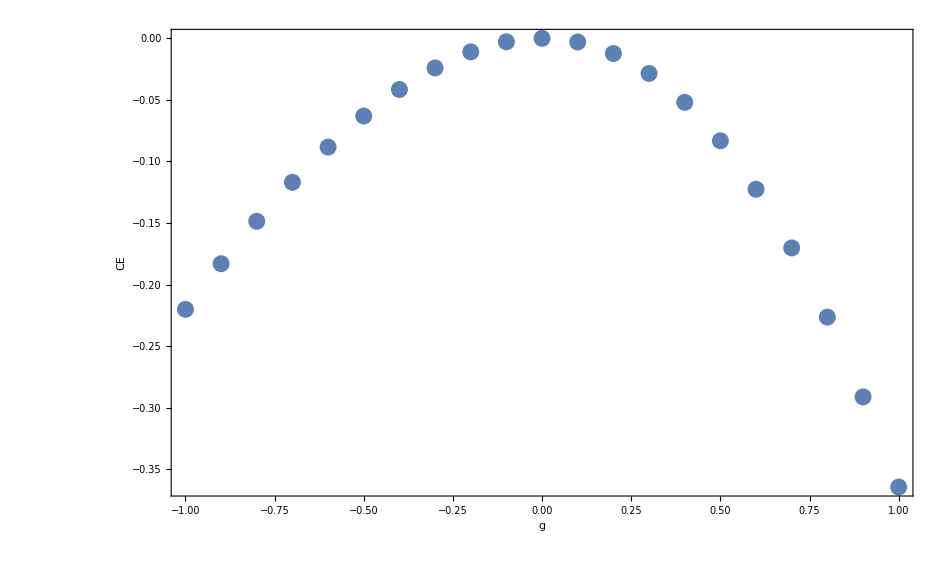

```mathematica
Show[ListPlot[CorrelationEnergy],Frame->True,FrameLabel->{"g","CE"}]
```